```mathematica
(*Problem 2*)
```

```mathematica
(*Lagrangian*)
```

```mathematica
L = (m/2)*(D[x[t],t]^2+D[y[t],t]^2+D[z[t],t]^2)
```

1/2 m (x'[t]^2+y'[t]^2+z'[t]^2)

```mathematica
cyl={x[t]->b*z[t]*Cos[a*z[t]],y[t]->b*z[t]*Sin[a*z[t]] ,z[t]->z[t],
D[x[t],t]->D[b*z[t]*Cos[a*z[t]],t],D[y[t],t]->D[b*z[t]*Sin[a*z[t]],t] };
```

```mathematica
L = L/.cyl//FullSimplify
```

1/2 m (1+b^2+a^2 b^2 z[t]^2) z'[t]^2

```mathematica
(*Euler-Lagrange Equation for z*)
```

```mathematica
FullSimplify[D[D[L,z'[t]],t] == D[L,z[t]]]
```

a^2 b^2 m z[t] z'[t]^2+m (1+b^2+a^2 b^2 z[t]^2) z''[t]==0

```mathematica
Solve[FullSimplify[D[D[L,z'[t]],t] == D[L,z[t]]],z''[t]]
```

{{z''[t]→-(a^2 b^2 z[t] z'[t]^2)/(1+b^2+a^2 b^2 z[t]^2)}}

```mathematica
Integrate[-(a^2 b^2 z[t])/(1+b^2+a^2 b^2 z[t]^2),z[t]]
```

-1/2 Log[1+b^2+a^2 b^2 z[t]^2]

```mathematica
zPrime[t]=v0*Sqrt[(1+b^2+a^2*b^2*h^2)/(1+b^2+a^2*b^2*z[t]^2)]
```

v0 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2))

```mathematica
(*Torque in two ways*)
```

```mathematica
q=m*b^2*a*D[z[t]^2*z'[t],t]/.{z''[t]->-(a^2 b^2 z[t] z'[t]^2)/(1+b^2+a^2 b^2 z[t]^2),z'[t]->v0 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2))}//FullSimplify
```

(a b^2 m (2 (1+b^2 (1+a^2 h^2)) v0^2 z[t]-a^2 b^2 z[t]^3 z'[t]^2))/(1+b^2+a^2 b^2 z[t]^2)

```mathematica
q/.{z'[t]->v0 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2))}//Simplify
```

(a b^2 (1+b^2 (1+a^2 h^2)) m v0^2 z[t] (2+2 b^2+a^2 b^2 z[t]^2))/((1+b^2+a^2 b^2 z[t]^2)^2)

```mathematica
AngMom=FullSimplify[m*Cross[{x[t],y[t],z[t]},{D[x[t],t],D[y[t],t],D[z[t],t] }]/.cyl/.{z'[t]->zPrime[t]}]
```

{-a b m v0 Cos[a z[t]] z[t]^2 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2)),-a b m v0 Sin[a z[t]] z[t]^2 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2)),a b^2 m v0 z[t]^2 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2))}

```mathematica
DAngMomZ=D[AngMom[[3]],t]//FullSimplify
```

(a b^2 m v0 z[t] ((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2))^(3/2) (2+2 b^2+a^2 b^2 z[t]^2) z'[t])/(1+b^2 (1+a^2 h^2))

```mathematica
DAngMomZ/.{z'[t]->v0 √((1+b^2+a^2 b^2 h^2)/(1+b^2+a^2 b^2 z[t]^2))}//FullSimplify
```

(a b^2 (1+b^2 (1+a^2 h^2)) m v0^2 z[t] (2+2 b^2+a^2 b^2 z[t]^2))/((1+b^2+a^2 b^2 z[t]^2)^2)

```mathematica
D[z^2/Sqrt[C+z^2],z]//FullSimplify
```

(2 C z+z^3)/((C+z^2)^(3/2))

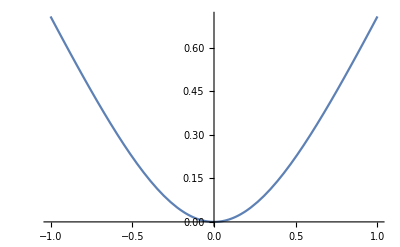

```mathematica
Plot[z^2/Sqrt[1+z^2],{z,-1,1}]
```

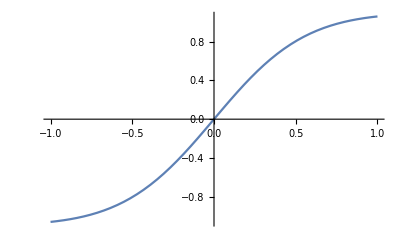

```mathematica
Plot[(2  z+z^3)/((1+z^2)^(3/2)),{z,-1,1}]
```